# Math 334: Differential Equations

## Exam 1 Review

## Chapter 1: Introduction

### Section 1.1: Some Basic Mathematical Models and Direction Fields

Differential equations are simply equations involving derivatives.

Many things in life and nature in involve relationships and the rate at which those relationships change. Mathematically, these relationships are defined by equations and the rate at which they change are defined by derivatives.

A direction field is a plot that contains small arrow at every point and these arrows show the slope of the underlying function at every point.

An Equilibrium solution is one that shows the dependent variable staying constant at the independent one changing (often it is y held constant with a change in time). These are where the derivative of the dependent variable is 0 and the direction field will show horizontal lines as you move down the horizontal axis.

Steps to constructing a mathematical model

Identify the independent and dependent variables and assign letters to represent them. Often an independent variable is time.

Choose the units of measurement for each variable. Try to make them as convenient as possible.

Discover the basic underlying principle or law behind what you are trying to model.

Express the principle or law in terms of your variables chosen in step 1

Make sure that the units match up when you solve the equation

### Section 1.2: Solutions of Some Differential Equations

An initial condition is the value of all your Variables at a specific instance. Often this will be at t=0.

The solving of a differential equation subject to initial conditions is called the initial value problem and is abbreviated I.V.P.

A general solution is one that contains all possible solutions to a differential equation, subject on some values for arbitrary constants c_1...ect.

The graphical representation of the general solution and that is called a family of integral curves. This is simply a plot containing multiple lines, each defined by choosing a different value for your constants.

### Section 1.3: Classification of Differential Equations

Ordinary Differential equations (ODE’s) are where your dependent variable only depends on one independent variable and there for you have only ordinary derivatives in your equation (no partials)

A partial differential equation (PDE’s) is where you have partial derivatives.

The order of a differential equation is simply the same as the highest order derivative you have in the equation.

A differential equation is linear if there are only linear terms in the equation. This one is a little fuzzy, but I know that if I see something like yy’ it isn’t linear. Also if you have a differential equation ∂y/∂t and somewhere you see the product of y and a different

## Chapter 2:First Order Differential Equations

### Section 2.1: Linear Equations; Method of Integrating Factors

There are various algorithms that will make the solving of first order linear differential equations much easier, but in order to apply them you need to express the equation in “standard form”: ⅆy/ⅆt+p(t)*y  g(t).

In order to solve an equation in standard form we will often need to alter the equation by multiplying the entire thing by a integrating factor μ(t). We would like to choose μ(t) so that we end up getting the entire left side of the equation being the derivative of something. So we want ⅆy/ⅆt+p(t)*y   to be equal to d/dt[μ(t)*y]

We know from the chain rule that ⅆy/ⅆt+p(t)*y  = μ(t)dy/dt+(dμ(t))/dt y. Upon examination we can see that (dμ(t))/dt=p(t) *μ(t).

Algebra says (dμ(t)/dt)/(μ(t))=p(t) → d/dt[ln|μ(t)| = p(t) → μ(t) = Exp[∫p(t) dt]

Now the general form with an integrating factor is μ(t) dy/dt+μ(t)p(t)y=μ(t)g(t)

Using what we know about the integrating factor we have d/dt[μ(t)y]=μ(t)g(t)→ μ(t)y = ∫μ(t)g(t)dt→y = 1/(μ(t))∫μ(t)g(t) dt

### Section 2.2: Separable Equations

A differential equation is called separable if we can write it in the form M(x,y)+N(x,y)dy/dx=0  or M(x,y)dx+N(x,y)dy=0

If an equation is separable it also means that you will be able to isolate all the x terms from the y terms and then just integrate both side to find your solution.

It is really easy to solve separable equations if they are written in this form dy/dx = (f(x))/(g(y))→ g(y)dy = f(x)dx→∫g(y)dy = ∫f(x)dx

### Section 2.3: Modeling with First Order Equations

Steps to modeling with first order equations

Generate a model using the steps from section 1.1

Analysis of the model: this is where you are actually presented with the problem of solving the differential equation.

Compare results with experimental results or observation: After you have found mathematical solutions to your model you need to test the validity of your model and make sure that it holds up.

The Tank Problem

A lot of problems in first order linear differential equations involve a reservoir of some type with a rate of inflow to the reservoir and a rate of outflow out of the reservoir.

This is an example problem and the steps to solving it: At time t = 0 a tank contains Q_0 lb of salt dissolved in 100 gal of water. Assume that water containing 1/4 lb of salt/gal is entering the tank at a rate of r gam/min and that he well-mixed solution is draining at the same rate. Write a model that will help you determine the amount of salt Q(t) at any moment in time.

dQ/dt = rate in - rate out = r/4-(r*Q)/100, Q(0)=Q_0

This is a linear equation and can therefore be solved using the method of an integrating factor where μ(t) = e^(rt/100).

Q(t)  = e^(-rt/100)*∫e^(rt/100)*r/4 dt=25 + ce^(-rt/100)

It can be verified that using the initial condition you get c = Q_0-25

This makes the solution to the IVP Q(t) = 25+ (Q_0-25)e^(-rt/100)

### Section 2.4: Differences Between Linear and Nonlinear Equations

THEOREM 2.4.1: If the functions p and g are continuous on an open interval I:α<t<β containing the point t = t_o, then there exists a unique function y = ϕ(t) that satisfies the differential equation y’ + p(t)y = g(t) for each t in I.

THEOREM 2.4.2: Let the functions f and ∂f/∂y be continuous in some rectangle α < t < β, γ < y < δ containing the point (t_0,y_0). Then in some interval t_o-h < t < t_0 + h contained in α < t < β, there is a unique solution y = ϕ(t) of the initial value problem y’ =  f(y,t), y(0) =t_0.

Sometimes you will not be able to do an integral or have some other obstacle that prevents you from solving for y directly. That is ok . Go as far as you can and when you are done simplifying you will get what is called the implicit solution. The explicit solution is preferable and is in the form y = f(t)

Summary of properties of Linear differential Equations of the form y’ + p(t)y = g(t)

On the interval where the Coefficient functions p(t) and g(t) are continuous there is a solution contain a constant c that is  the general solution to the differential equation.

There is an explicit solution to the differential equation.

The points of discontinuity can be seen before solving the problem by looking at possible points of discontinuity in the coefficient functions p(t) and g(t).

### Section 2.5: Autonomous Equations and Population Dynamics

An autonomous equation is one in which the independent variable doesn't appear explicit in the original differential equation, thus it has form dy/dt = f(y). (in this case the independent variable is t and its only appearance is in the derivative term)

These types of equations are common in economics and population growth studies.

For graphically understanding the behavior of the solutions without solving the equation we have a few tools:

Because these equations are written at dy/dt = f(y) it is helpful to draw a plot of f(y) vs y. The first step in doing this is to find the critical points  or roots (zeros) of f(y). We can then choose values in between critical points and see if the curve comes from above or below to meet the critical point on the horizontal (y in this case) axis. If it comes from above we will be able to know that the solutions are increasing on the interval between the critical points and if it comes from below we know that they are decreasing. (We usually draw lines on the axis to show direction so if the it is above the y line we draw an arrow on the axis to the right and it is below we draw a line to the left on the axis..)

The phase line is just a vertical line representing the y axis where the arrows we hinted at above are shown.  This will allow us to determine the characteristics of the equilibrium solutions identified from our plot of f(y) and y. There are three possibilities and they are summarized as follows: One arrow in and one out | Both out | Both in
semi-stable | unstable | Asomptotically Stable

Finally we can plot some sample solutions of our equation on a graph of y vs. t. We start by drawing horizontal lines at all of our Equilibrium solutions and then using the phase line to determine whether the in between starting points head to a particular critical point or away from them. We determine changes in concavity of our solution line by looking at the second derivative of y. This is also the first derivative of f(y) because of how the differential equation is written. On our graph of f(y) vs y we will see these changes in concavity as points of inflection (change from heading up to down).

Example dy/dt = y^3-2 y^2-3y→ y(y-3)(y+1), zeros are -1,0,3

```mathematica
Plot[y^3-2y^2-3y,{y,-2,5}];
Solve[D[y^3-2y^2-3y,y]==0,y]//N
```

{{y→-0.535184},{y→1.86852}}

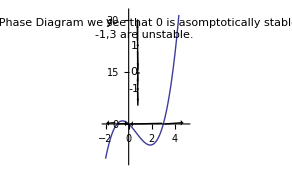
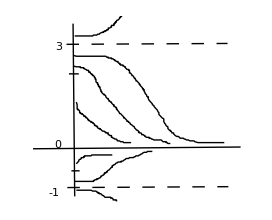

Types of Autonomous equations and their solutions

Exponential growth or decay:

dy/dt = ry and y(0) = y_0, where r is the rate of growth or decay.

This is a separable equation and we get dy/y= r dt → ∫1/y dy = ∫r dt → ln[y] = rt +c→y = ce^rt→ y = y_0 e^rt

These types of solutions aren’t always realistic because they imply that there is room for y to grow very quickly as t increases without ever hitting a ceiling of sorts.

Logistic Growth or decay: Similar to the exponential, but they account for the fact that the growth rate actually depends on the current value of the population.

dy/dt = h(y)y

We want h(y) to be about equal to r when y is small and we want it to decrease as y gets bugger so the best way to do that is to say that h(y) = r-ay where r is the growth rate in the absence of limiting factor and a is a positive constant

dy/dt = (r-ay)y→ dy/dt = r(1-y/K) where K = r/a

We want to look for equilibrium or constant solutions, those are where there is no change or dy/dt =0, this can be written r(1-y/K)y = 0. They are also known as critical points.

In this case K is called the carrying capacity or the saturation level. It is actually an equilibrium solution to the differential equation.

You will probably have to do partial fractions here, but the solution works out to be:

y = (K y_0)/(y_0 + (K - y_0)e^-rt)

Logistic Growth with a Thresh hold: Combines the ideas from both of them to say you have a threshold like before, but that you also have a factor that makes dy/dt negative when y is large so it decreases down to the threshold, rather than just increasing.

dy/dt=-r (1-y/T)(1-y/K)y There will be three circuital points, y=0,T,K

The solution to this equation will depend on the actual problem, but it is in form.

### Section 2.6: Exact Equations and Integrating Factors

An Equation is said to be exact if it can be written in the form M(x,y) + N(x,y) y’ =0 Where (∂M)/(∂y)=(∂N)/(∂x).

We don’t know how to solve these all the time so we need to learn a new trick. Let’s say that (∂ψ)/(∂x)=M(x,y) and (∂ψ)/(∂y)= N(x,y)

If that is the case M(x,y) + N(x,y) y’ = d/dx ψ{x,ϕ(x)]=0

We now have a two step problem to finding out what ψ is:

We know that ψ_x=m→ψ=∫M dx +g(y) //in this case the constant of integration is a function of the other variable in our integrand. That is noted as g(y)

we also know that ψ_y=N

We write that in the middle  and expand in this way d/dyψ = ∫M dx + g(y)=ψ_y=N(x,y). We should see that everything with an x is canceling in the ψ part except g’(y) and we will get that is either equal to a constant (sometimes 0) or a function of only y. We then integrate that and get g(y)

With g(y) we go back to ψ = ∫mdx + g(y) = c and that is our solution.

If M_y≠N_x there might exist an integrating factor μ such that (μM)_y=(μN)_x→ μ_y M + μM_y = μ_x N + μN_x (* this is by the product rule  *)

For this class we will assume that μ is either only a function of x or only a function of y.

If we asume that μ is only a function of x we know that μ_y=0 and we can solve for μ and show that μ(x) = Exp[∫(M_x-N_y)/N dx]

By the same logic μ as a function of y can be found t o be μ(y) = Exp[∫(N_y-M_x)/M dy]

After that we multiplly everything through by μ and solve for ψ using the algorithm above.

## Equations or things to remember for solving Different types of eqns.

### Linear First order equations

dy/dt+p(t)y = g(t)

μ(t) = Exp[∫p(t) dt]

y = 1/(μ(t))[∫μ(t)g(t)dt +c]

### Separable First order equations

M(x,y) dx + N(x,y)dy = 0 or M(x,y)+N(x,y)dy/dx=0 or the most useful dy/dx=(f(x))/(g(y))

g(y)dy = f(x)dx

∫g(y)dy = ∫f(x)dx +c→ algebra gets you y = f(x)

### Autonomous Equations (population dynamics)

dy/dt = f(y) (* t doesn’t appear explicit in our differential equation)

Get an idea of what it looks like by plotting f(y) vs y, the phase line, and some sample solutions (name critical points as semi-stable, unstable, or asymptotically stable*)

#### Exponential Growth or Decay

dy/dt = ry and y(0) = y_0, where r is the rate of growth or decay.

This is a separable equation and we get dy/y= r dt → ∫1/y dy = ∫r dt → ln[y] = rt +c→y = ce^rt→ y = y_0 e^rt

y = y_0 e^rt

#### Logistic Growth or Decay

dy/dt = h(y)y = r(1-y/K), K = r/a, a is positive constant

Carrying capacity is K

y = (K y_0)/(y_0 + (K - y_0)e^-rt)

#### Logistic Growth with a Threshold

dy/dt=-r (1-y/T)(1-y/K)y

Critical points are y = 0, y = T, y = K

Solve probably using Partial Fraction Integration

### Exact Equations

M(x,y)dx + N(x,y)dy = 0 or M(x,y) + N(x,y) dy/dx=0

Check to see if M_y=N_x (subscripts mean partial derivatives). If so the equation is exact. If not see below for help to find integrating factor

(∂ψ)/(∂x)=M(x,y) and (∂ψ)/(∂y)= N(x,y)

ψ = ∫ M dx + g(y)

d/dy[∫M dx + g(y)] = ψ_y=  N // all x’s should drop out when you equate ψ_y=N. If not you did it wrong. This lets you integrate to solve for g(y). You have to integrate because in doing the derivative of the ∫  you get a g’(y).

The solution is ∫M(x,y) dx + g(y) = c

Finding an Integrating Factor (* note that for this class our integrating factors will always be functions of only one vairable *)

If we want an integrating factor as a function of x, μ(x) = Exp[∫(M_x-N_y)/N dx]. We will be able to tell before we do the integration if this is what we want because all the y’s will have to drop out of the (M_x-N_y)/N in order to get a function of only x out of the integral.

If we want an integrating factor as a function of y, μ(y) = Exp∫(N_y-M_x)/M dy] We will be able to tell before we do the integration if this is what we want because all the x’s will have to drop out of the (N_y-M_x)/M in order to get a function of only x out of the integral.

## Integrals Expected to have Known

∫sin[ax]dx = (-cos[ax])/a + C

∫cos[ax]dx = sin[ax]/a + C

∫e^ax dx = 1/a e^ax+C

∫sec[x] dx = ln |sec x +tan x| + C

∫ csc x dx = ln|scsx - cot x| + C = - ln |csc x +cot x| +C

∫ tan x dx = -ln|cos x| + C

∫ cot x dx  = ln |sin x| + C

∫ ln |x| = xln|x| -x +C

∫dx/(a^2+x^2)= 1/a artcan [x/a] + C

∫dx/(√(a^2-x^2))= arcsin[x/a] +C

∫e^ax sin[bx] dx = (e^ax(a sin[bx] - bcos[bx]))/(a^2+b^2)

∫e^ax cos[bx] dx = (e^ax(b sin[bx] + a cos[bx]))/(a^2+b^2)

∫sin^2[mx] dx = (mx - sin[mx]cos[mx])/(2m)

∫cos^2[mx] = (mx + sin[mx] cos[mx])/(2m)